```mathematica
backgroundsolution[args_]:= Module[
{startI = 0.000001,
endI = 1.001,
startE = 1,
endE = 1000,
Λ = .010,
ϕcosmological = .1,
ρ = 10,
Rscaled = 1},
Shooter = args[[2]];
ϕ0 = args[[1]];
backgroundsolutioninterior= NDSolve[{1/Rscaled^2 D[ϕ[r],r,r]+2/(r Rscaled)D[ϕ[r],r]+2/Λ^2(4/(r Rscaled)D[ϕ[r],r]+ 2/(r^2 Rscaled^2)(D[ϕ[r],r])^2)==8π ρ,ϕ'[startI] ==0,ϕ[startI] ==  ϕ0},
ϕ,{r,startI,endI}];
backgroundsolutionexterior=NDSolve[{1/Rscaled^2 D[ϕe[r],r,r]+2/(r Rscaled)D[ϕe[r],r]+2/Λ^2(4/(r Rscaled)D[ϕe[r],r]+ 2/(r^2 Rscaled^2)(D[ϕe[r],r])^2)==0,ϕe[startE] ==  ϕ[1]/.backgroundsolutioninterior,ϕe'[startE] == ϕ'[1]/.backgroundsolutioninterior},
ϕe,{r,startE,endE}];
Proximity= (ϕe[endE]/.backgroundsolutionexterior) -ϕcosmological;
If[Shooter,Prepend[Proximity,ϕ0],{backgroundsolutioninterior,backgroundsolutionexterior}]
]
```

```mathematica
Solutions = Table[backgroundsolution[{x,True}],{x,Range[Trialstart,Trialend,Trialstep]}];
```

```mathematica
(*Solutions = Parallelize[Table[backgroundsolution[{x,True}],{x,Range[Trialstart,Trialend,Trialstep]}]];*)
```

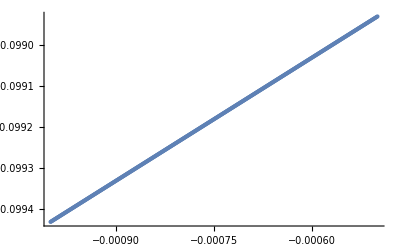

```mathematica
With[{Trialend = -.0005,
Trialstart = -.001,
Trialstep = .000001},ListPlot[Table[backgroundsolution[{x,True}],{x,Range[Trialstart,Trialend,Trialstep]}]]]
```

```mathematica
sol=backgroundsolutionShooter[{.1,False}]
```

{{{ϕ→                             -6
InterpolatingFunction[{{1. 10  , 1.001}}, <>]}},{{ϕe→InterpolatingFunction[{{1., 1000.}}, <>]}}}

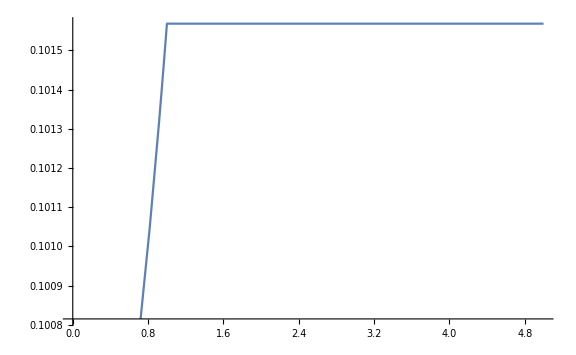

```mathematica
Plot[Piecewise[{{ϕ[r]/.sol[[1]],r<1},{ϕe[r]/.sol[[2]],r>1}}],{r,.0001,5},ImageSize->Large]
```

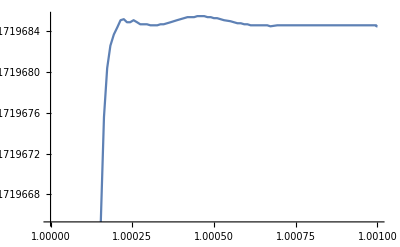

```mathematica
Plot[ϕe[r]/.sol[[2]],{r,1,1.001}]
```